```mathematica
(* Copyright (C) 2020 Craciun Alexandru

This package is free: you can redistribute it and/or modify it under the
 terms of the GNU General Public License as published by the Free Software
 Foundation, either version 3 of the License, or (at your option) any
 later version. This program is distributed in the hope that it will be
 useful, but WITHOUT ANY WARRANTY; without even the implied warranty of
 MERCHANTABILITY or FITNESS FOR A PARTICULAR PURPOSE. See the GNU General
 Public License for more details. You should have received a copy of the
 GNU General Public License along with this program
if not, see <https://www.gnu.org/licenses/>.

 Author: CRACIUN Alexandru, e-mail:alexandru.craciun@inflpr.ro

 Please send me an e-mail if you have found a mistake or have questions. *)
(*This is an updated supplementary material for the paper:  
[11]. A.Craciun, and T.Dascalu, "A method to generate vector beams with adjustable amplitude in the focal plane," Appl.Sci.10,2313 (2020). *)
(*The approach is slightly different from that in the paper, namely, instead of using the +/- circularly polarized modes to represent the E. Field 
in the plane of the lens (before the focus), it uses the Azimuthally (A) and Radially (R) polarized modes. This allows us to trace differently
the Ordinary and Extraordinary polarizations each with a set of rays instead of one set of rays with the phase difference between E/O polarization computed for each ray. *)

(*This code is compatible with Mathematica 10 or later versions.*)

(*Mathematica is (C) Copyright 1988-2020 Wolfram Research, Inc. 
Protected by copyright law and international treaties. 
Unauthorized reproduction or distribution subject to severe civil and criminal penalties.
Mathematica is a registered trademark of Wolfram Research, Inc. 
*)
```

```mathematica
(*Some Vector Graphics were replaced by Images to decrease the file size. *)
SetOptions[EvaluationNotebook[],AutoStyleOptions->{"CommentStyle"->{FontWeight->Plain,FontColor->Darker[Red],ShowAutoStyles->False,ShowSyntaxStyles->False,AutoNumberFormatting->False,FontFamily->"Consolas"}}]
```

```mathematica
(*     - Parameters of the optical system*)

embeddedCompLength=12. mm; (*This is the distance between start point of the system and the apex of the second surface of MC.*)
apexsDistance=9.mm;(*This is the distance between the two apexes of the componet MC.*)
coneAngle=7.0;(*This is the cone angle of the conical surface for the first version of MC.*)
CR1=5.0mm;(*This is the curvature radius of the tip of the front surface of the MC*)
CR2=5.57mm;(*This is the start point for the curvature radius of the tip of the back surface of the MC*)
refractiveIndexO=1.76013;(*Ordinary refractive index of MC (Saphire).*)
refractiveIndexE=1.75220;(*Extraordinary refractive index of MC (Saphire).*)

nth[θ_]=Sqrt[1/(Cos[θ]^2/refractiveIndexO^2+Sin[θ]^2/refractiveIndexE^2)];(*θ dependent refractive index, where θ is the tilt angle of the rays with respect to optical axis.*)
fr=FindRoot[Sin[coneAngle/180.*Pi-th]^2/Sin[coneAngle/180.*Pi]^2==Cos[th]^2/refractiveIndexO^2+Sin[th]^2/refractiveIndexE^2,{th,coneAngle/180.*Pi/2}];
refractiveIndex=(nth[th]/.fr)/2+refractiveIndexO/2;(*This is the refractive index of MC as will be used for optimization purposes, assumes that E ray and O ray have the same path. Is correct for a ray far from the tip of the MC.*)
distancetoLens=50. mm; (*This is the distance considered between MC and lens. !!!!! in [11] this distantce is 150 mm. *)
focalDistance=18.00mm;(*This is a presumable good start point for the back focal length of the high NA asphere considered for the simulations.*)
focalDistance=18.9788544185mm;(*This gives the correct value of the back focal length as given by FindFocus.*)
centerThicknessLens=9. mm;(*This is the center thickness for the high NA asphere.*)
refractiveIndexLens=1.7761;(*This is the refractive index of the high NA asphere(S-LAH64) from https://refractiveindex.info/?shelf=glass&book=OHARA-LAH&page=S-LAH64 .*)

(*     - List interface functions and derivatives.*)
surface1b[x_,y_]=-CR1/Cot[coneAngle/180*Pi]^2-SLz[x,y,CR1,-(1+Cot[coneAngle/180*Pi]^2)]+embeddedCompLength-apexsDistance;
surface2b[x_,y_]=-CR2/Cot[coneAngle/180*Pi]^2-SLz[x,y,CR2,-(1+Cot[coneAngle/180*Pi]^2)]+embeddedCompLength;(*StartDesign Surface*)
DxSurface1[x_,y_]=D[surface1b[x,y],x];
DySurface1[x_,y_]=D[surface1b[x,y],y];
(*-Graphics-*)
KK[x_,Dxs_]:=refractiveIndex(Dxs^2+1);
rho[x_,Dxs_]:=Dxs(1-Sqrt[refractiveIndex*KK[x,Dxs]-Dxs^2])/KK[x,Dxs];
xi[x_,Dxs_]:=(Dxs^2+Sqrt[refractiveIndex*KK[x,Dxs]-Dxs^2])/KK[x,Dxs];
xa=Sort@Join[t=Table[x,{x,0.92 mm,13 mm,0.002 mm}];-t,t];
za=Map[surface1b[#,0]&,xa];
Dxs=Map[DxSurface1[#,0]&,xa];
zbI=Map[surface2b[#,0]&,xa];
zb=(za +(1-refractiveIndex)*(apexsDistance-0.02 mm-0.008 mm-0.0015 mm)*MapThread[xi[#1,#2]&,{xa,Dxs}]/(MapThread[xi[#1,#2]&,{xa,Dxs}]-refractiveIndex));
xb=xa+(zb-za)MapThread[rho[#1,#2]&,{xa,Dxs}]/MapThread[xi[#1,#2]&,{xa,Dxs}];
surface2b[x_,y_]=Interpolation[Transpose[{xb,zb}],InterpolationOrder->6][Sqrt[x^2+y^2]];(*The Ideal Surface to generate a colimated beam, according to the equations from:
[12]. Rafael G.Gonzalez-Acuña and Julio C.Guitiérrez-Vega, "Generalization of the axicon shape: the gaxicon," J.Opt.Soc.Am.A 35,1915-1918 (2018).*)

ff=FindFit[
Transpose[{xb,zb}],
c[0]+c[1] x^2+c[2] x^4+c[3] x^6+c[4] x^8+c[5] x^10+c[6] x^12+c[7] x^14+c[8] x^16-(x^2/R)/(1+√(1-(1+Ck)x^2/R^2)),

{{R,0.0076},{Ck,-36.365},{c[0],0.01},{c[1],8.3},{c[2],-169000.},{c[3],3.71*^9},{c[4],-5.82*^13},{c[5],5.9*^17},{c[6],-3.76*^21},{c[7],1.32*^25},{c[8],-1.97*^28}},x,MaxIterations->5000];(*This fit the Ideal Surface with an aspherical surface function.*)
Print[" The equation of the first surface of the MC1: "];
Print[surface1b[x,y]];
Print["The equation of the second surface of the MC1: "]
Print[surface2b[x_,y_]=(c[0]+c[1] (x^2+y^2)+c[2] (x^2+y^2)^2+c[3] (x^2+y^2)^3+c[4] (x^2+y^2)^4+c[5] (x^2+y^2)^5+c[6] (x^2+y^2)^6+c[7] (x^2+y^2)^7+c[8] (x^2+y^2)^8-((x^2+y^2)/R)/(1+√(1-(1+Ck)(x^2+y^2)/R^2)))/.ff];(*Here is the second surface of the component MC.*)



surface1[x_,y_]=If[√(x^2+y^2)≤  13 mm,surface1b[x,y],-CR1/Cot[coneAngle/180*Pi]^2-SLz[x,y,CR1,-(1+Cot[coneAngle/180*Pi]^2)]+embeddedCompLength-apexsDistance];
surface2[x_,y_]=If[√(x^2+y^2)≤  13 mm,surface2b[x,y],-CR2/Cot[coneAngle/180*Pi]^2-SLz[x,y,CR2,-(1+Cot[coneAngle/180*Pi]^2)]+embeddedCompLength];
surface3[x_,y_]=ALz[x,y,18.651mm,-1.408,{0,1.4755 10^(-5),-5.557 10^(-9),-3.511  10^(-12),0,0,0,0}]+distancetoLens+embeddedCompLength;(*This is the front surface for the high NA asphere.*)
surface4[x_,y_]=+embeddedCompLength+distancetoLens+centerThicknessLens;

DxSurface1[x_,y_]=D[surface1[x,y],x];
DySurface1[x_,y_]=D[surface1[x,y],y];
DxSurface2[x_,y_]=D[surface2[x,y],x];(*Slopes of the interfaces: needed for ray tracing.*)
DySurface2[x_,y_]=D[surface2[x,y],y];
DxSurface3[x_,y_]=D[surface3[x,y],x];
DySurface3[x_,y_]=D[surface3[x,y],y];
DxSurface4[x_,y_]=D[surface4[x,y],x];
DySurface4[x_,y_]=D[surface4[x,y],y];
```

The equation of the first surface of the MC1:

0.00292462-(200. (x^2+y^2))/(1+√(1+2.65322×10^6 (x^2+y^2)))

The equation of the second surface of the MC1:

0.0118992+2.07587 (x^2+y^2)-30078.2 (x^2+y^2)^2+4.85691×10^8 (x^2+y^2)^3-5.70503×10^12 (x^2+y^2)^4+4.4459×10^16 (x^2+y^2)^5-2.15821×10^20 (x^2+y^2)^6+5.87886×10^23 (x^2+y^2)^7-6.84302×10^26 (x^2+y^2)^8-(134.221 (x^2+y^2))/(1+√(1+968139. (x^2+y^2)))

```mathematica
(*The definition of the optical system for O rays.*)

optSystemO[rayCoordinateStart_,focusCorrection_]:=Module[{},(*When called this function trace the rays through the system and compute the intersections with the surfaces and directions for each O. ray. *)
(*This function uses global variables, which are changed by the function and then used in the program. *)
rayTiltStart={0,0,1}&/@rayCoordinateStart;
(*All Start rays are paralel to the optical axis. *)
intersection0=Map[{#[[1]],#[[2]],0}&,rayCoordinateStart];
(*Dummy plane surface. *)
intersection1= SurfaceIntersection[intersection0,{},rayTiltStart][surface1,DxSurface1,DySurface1];(*This is the intersection with the first surface. *)
(*The result is exact in one iteration for rays parallel with the optical axis or for a plane interfaces. *)
direction1= DirectionIn[intersection1,rayTiltStart,refractiveIndex][DxSurface1,DySurface1];
(*This is the direction vectors for the O. rays in the MC crystal. *)
intersection2= SurfaceIntersection[intersection1,{},direction1][surface2,DxSurface2,DySurface2];
Do[intersection2= SurfaceIntersection[intersection2,{},direction1][surface2,DxSurface2,DySurface2];,10];(*This is the intersection with the second surface. *)
(*We need multiple iterations to achieve convergence.*)
direction2= DirectionOut[intersection2,direction1,refractiveIndexO][DxSurface2,DySurface2];
(*The direction of the rays between MC and the lens. *)
intersectionA= SurfaceIntersection[intersection2,{},direction2][surface2[0,0]&,0&,0&];
(*Dummy plane surface tangent to the MC. *)
intersectionB= SurfaceIntersection[intersection2,{},direction2][surface3[0,0]&,0&,0&];
(*Dummy plane surface tangent to the front face of the lens. *)
intersection3= SurfaceIntersection[intersection2,{},direction2][surface3,DxSurface3,DySurface3];
Do[intersection3= SurfaceIntersection[intersection3,{},direction2][surface3,DxSurface3,DySurface3];,10];

direction3= DirectionIn[intersection3,direction2,refractiveIndexLens][DxSurface3,DySurface3];

intersection4= SurfaceIntersection[intersection3,{},direction3][surface4,DxSurface4,DySurface4];

direction4= DirectionOut[intersection4,direction3,refractiveIndexLens][DxSurface4,DySurface4];

intersection5= SurfaceIntersection[intersection4,{},direction4][(surface4[0,0]+focalDistance)&,0&,0&];

direction5=direction4;

rayCoordinateEnd=Map[#[[{1,2}]]&,intersection4];

rayTiltEnd=Map[#[[{1,2}]]&,direction4];

rayCoordinateFocus=Map[#[[{1,2}]]&,intersection5];

rayTiltFocus=rayTiltEnd;

pathLengthCrystal=FindOpticalPathLength[{intersection1,intersection2},{1}];

convEff=-k0*pathLengthCrystal*(refractiveIndexO-Map[nth,ArcCos[#[[3]]&/@direction1]]);(*This is the phase difference between ordinary and extraordinary ray, is necessary to compute the convesion efficiency along the ray.*)

]

optSystemE[rayCoordinateStart_,focusCorrection_]:=Module[{},(*When called this function trace the rays through the system and compute the intersections with the surfaces and directions for each E. ray. *)

rayTiltStart={0,0,1}&/@rayCoordinateStart;

intersection0=Map[{#[[1]],#[[2]],0}&,rayCoordinateStart];

intersection1= SurfaceIntersection[intersection0,{},rayTiltStart][surface1,DxSurface1,DySurface1];
direction1= DirectionIn[intersection1,rayTiltStart,refractiveIndexO][DxSurface1,DySurface1];
(*This is a Starting Guess direction for the E. rays in the MC. *)
Do[
thetaTab=Map[ArcCos[#[[3]]]&,direction1];
refractiveIndexTab=Map[nth,thetaTab];
direction1= DirectionIn[intersection1,rayTiltStart,refractiveIndexTab][DxSurface1,DySurface1];

,5];(*This part determines the direction of the Extraordinary rays in the crystal and E. refractive index for each ray, in an iterative process because these quantities depend on each other. *)

intersection2= SurfaceIntersection[intersection1,{},direction1][surface2,DxSurface2,DySurface2];
Do[intersection2= SurfaceIntersection[intersection2,{},direction1][surface2,DxSurface2,DySurface2];,10];

direction2= DirectionOut[intersection2,direction1,refractiveIndexTab][DxSurface2,DySurface2];

intersectionA= SurfaceIntersection[intersection2,{},direction2][surface2[0,0]&,0&,0&];

intersectionB= SurfaceIntersection[intersection2,{},direction2][surface3[0,0]&,0&,0&];

intersection3= SurfaceIntersection[intersection2,{},direction2][surface3,DxSurface3,DySurface3];
Do[intersection3= SurfaceIntersection[intersection3,{},direction2][surface3,DxSurface3,DySurface3];,10];

direction3= DirectionIn[intersection3,direction2,refractiveIndexLens][DxSurface3,DySurface3];

intersection4= SurfaceIntersection[intersection3,{},direction3][surface4,DxSurface4,DySurface4];

direction4= DirectionOut[intersection4,direction3,refractiveIndexLens][DxSurface4,DySurface4];

intersection5= SurfaceIntersection[intersection4,{},direction4][(surface4[0,0]+focalDistance)&,0&,0&];

direction5=direction4;

rayCoordinateEnd=Map[#[[{1,2}]]&,intersection4];

rayTiltEnd=Map[#[[{1,2}]]&,direction4];

rayCoordinateFocus=Map[#[[{1,2}]]&,intersection5];

rayTiltFocus=rayTiltEnd;


]
```

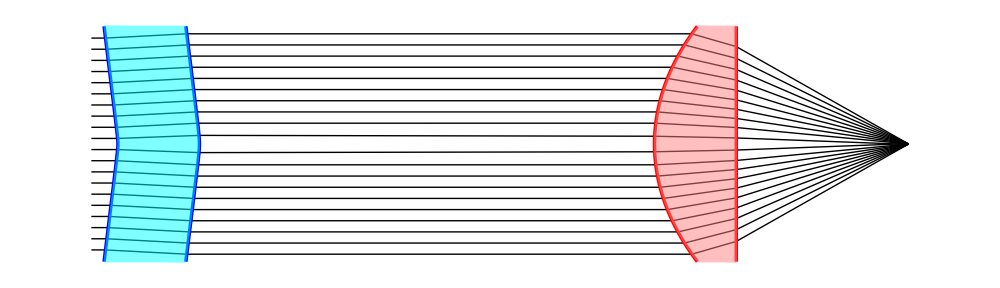

```mathematica
optSystemO[LineGrid[11.7 mm ,20],0];
llpO=ListLinePlot[Transpose[#[[All,{3,1}]]&/@{intersection0,intersection1,intersection2,intersection3,intersection4,intersection5}],Frame-> False,Axes-> False,AspectRatio->26 mm/(embeddedCompLength+distancetoLens+centerThicknessLens+focalDistance),PlotStyle->{{Thin,Black}}];
(*This part draw the rays.*)

Show[

llpO,
ListLinePlot[{Table[{surface1[x,0],x},{x,-13 mm ,13 mm,26 mm/200}],Table[{surface2[x,0],x},{x,-13 mm ,13 mm,26 mm/200}],Table[{surface3[x,0],x},{x,-13 mm ,13 mm,26 mm/200}],Table[{surface4[x,0],x},{x,-13 mm ,13 mm,26 mm/200}]},PlotStyle->{{Blue,Thickness[0.0025]},{Blue,Thickness[0.0025]},{Red,Thickness[0.0025]},{Red,Thickness[0.0025]}}],
(*This part draw the interfaces.*)
ListLinePlot[SortBy[Join[Table[{surface1[x,0],x},{x,-13 mm ,13 mm,26 mm/200}],Table[{surface2[x,0],x},{x,-13 mm ,13 mm,26 mm/200}]],Last],PlotStyle->{{Cyan,Thick,Opacity[0.5]},{Cyan,Thick},Black,Red},PlotRangePadding->0],
ListLinePlot[SortBy[Join[Table[{surface3[x,0],x},{x,-13 mm ,13 mm,26 mm/200}],Table[{surface4[x,0],x},{x,-13 mm ,13 mm,26 mm/200}]],Last],PlotStyle->{{Pink,Thick,Opacity[0.5]},{Pink,Thick},Black,Red},PlotRangePadding->0],
(*This part make the filling between interfaces.*)
ImageSize-> 1000,PlotRange-> All,ImagePadding-> Scaled[0.005]]

(*FIG. 1 - The Optical System. *)
```

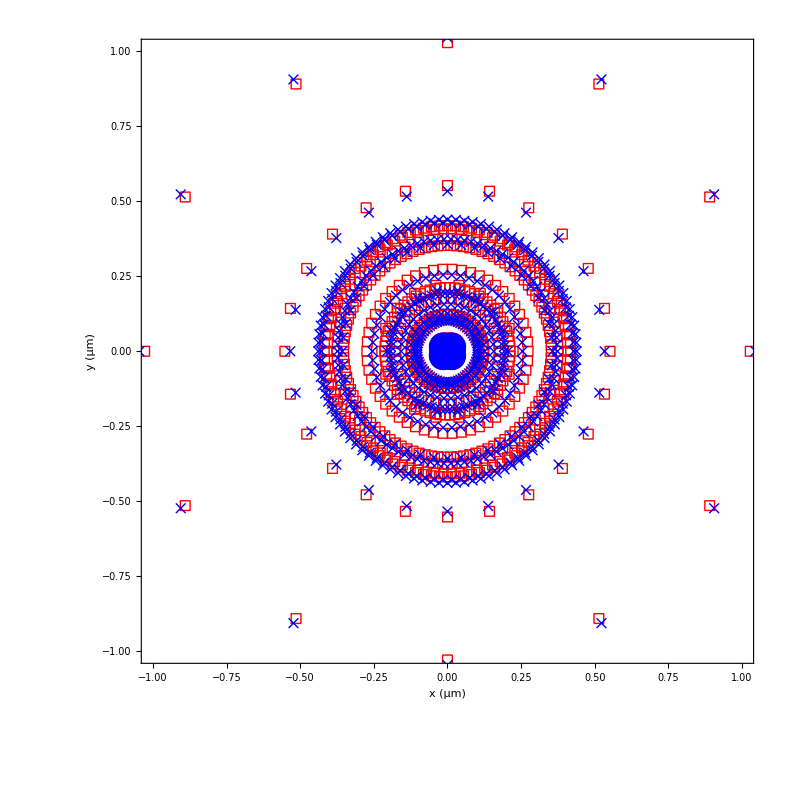

```mathematica
optSystemO[rayCoordinateStart=HexapolarGrid[11.7 mm ,17],0];
lppO=ListPlot[rayCoordinateFocus/um,PlotRangePadding->0,FrameLabel->{"x (μm)","y (μm)"},PlotMarkers->{"□",10},PlotRange-> {{-1,1},{-1,1}},PlotStyle->RGBColor[1, 0, 0]];(*Ordinary Rays*)
optSystemE[rayCoordinateStart,0];
lppE=ListPlot[rayCoordinateFocus/um,PlotRangePadding->0,FrameLabel->{"x (μm)","y (μm)"},PlotMarkers->{"×",10},PlotRange-> {{-1,1},{-1,1}},PlotStyle-> RGBColor[0, 0, 1]];(*Extraordinary Rays*)
Show[lppO,lppE](*We can see that E-Rays and O-Rays have nearly the same focal plane. This also shows us that the Focal Spot is nearly difraction limited. *)

(*FIG. 2 - Ray Intersection with the Focal Plane

Ordinary Rays(Red), Extraordinary Rays(Blue).
*)
```

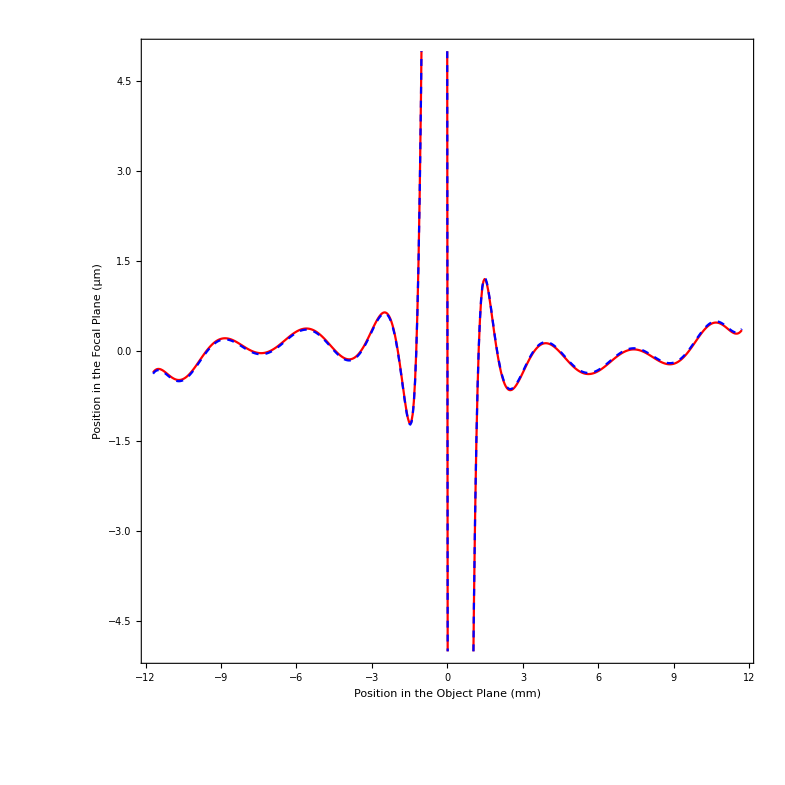

```mathematica
optSystemO[rayCoordinateStart=LineGrid[11.7 mm ,500],0];
lppO=ListLinePlot[Transpose[{#[[1]]&/@rayCoordinateStart/mm,#[[1]]&/@rayCoordinateFocus/um}],Frame->True,Axes->{True,False},AspectRatio->1,PlotRangePadding->Scaled[.05],FrameLabel->{"Position in the Object Plane (mm)","Position in the Focal Plane (μm)"},PlotRange->{-5,5},PlotStyle->RGBColor[1, 0, 0]];(*Ordinary Rays*)
optSystemE[rayCoordinateStart,0];
lppE=ListLinePlot[Transpose[{#[[1]]&/@rayCoordinateStart/mm,#[[1]]&/@rayCoordinateFocus/um}],Frame->True,Axes->{True,False},AspectRatio->1,PlotRangePadding->Scaled[.05],FrameLabel->{"Position in the Object Plane (mm)","Position in the Focal Plane (μm)"},PlotRange->{-5,5},PlotStyle-> {RGBColor[0, 0, 1],Dashed}];(*Extraordinary Rays*)

Show[lppO,lppE](*FIG. 3 - Ray Fan Diagram 
Ordinary Rays(Red), Extraordinary Rays(Blue). 
*)
```

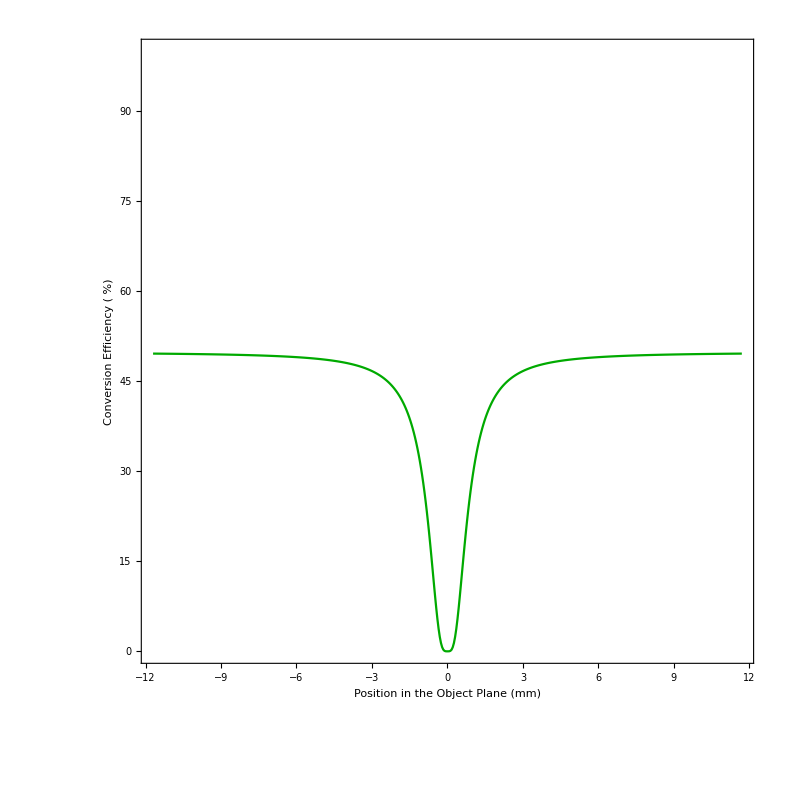

```mathematica
optSystemE[rayCoordinateStart,0];
ListLinePlot[Transpose[{#[[1]]&/@rayCoordinateStart/mm,100*Sin[convEff/2]^2}],Frame->True,Axes->{True,False},AspectRatio->1,PlotRangePadding->Scaled[.05],FrameLabel->{"Position in the Object Plane (mm)","Conversion Efficiency ( %)"},PlotRange->{0,100},PlotStyle->Darker@ Green]

(*FIG. 4 - Conversion Efficiency. *)
```

```mathematica
Wx=8 mm;(*This part may take @ 5 mins. *)
f1[x_,y_]=If[√(x^2+y^2)≥ 18 mm,0,If[x^2+y^2==0,0,Exp[-(x^2+y^2)/Wx^2-ⅈ ArcTan[x,y]]]];(*To avoid problems with the phase singularity, the intensity is zero along optical axis.*)
(*f1 -> incoming beam on SPP, which is placed at 1m away from MC. *)
(*This part does the propagation between SPP and MC using Angular Spectrum Propagator (Spectrum of Plane Waves). *)
f2=SPWOperator[18 mm,768,1.0,"padLevel"-> 2][f1];

optSystemO[CartesianGrid[12 mm,200],0];(*Trace the O. Rays*)

f3=AmplitudeGeometricOperator[intersection0,intersection4,"uniformGrid"-> True][f2];(*Compute the amplitude of the Azimuthally polarized mode after the lens. *)

optSystemE[CartesianGrid[12 mm,200],0];(*Trace the E. Rays*)

f3E=AmplitudeGeometricOperator[intersection0,intersection4,"uniformGrid"-> True][f2];(*Compute the amplitude of the Radially polarized mode after the lens. *)

opticalLengthO=FindOpticalPathLength[(*Optical path length for the O. rays (gives the phase of the Azimuthal beam). *)
{intersection0,intersection1,intersection2,intersection3,intersection4,intersection5},
{refIndexAir,refractiveIndexO,refIndexAir,refractiveIndexLens,refIndexAir}
];

opticalLengthE=FindOpticalPathLengthU[(*Optical path length for the E. rays (gives the phase of the Radially polarized beam). *)
{intersection0,intersection1,intersection2,intersection3,intersection4,intersection5},
{refIndexAir&/@refractiveIndexTab,refractiveIndexTab,refIndexAir&/@refractiveIndexTab,refractiveIndexLens&/@refractiveIndexTab,refIndexAir&/@refractiveIndexTab}
];
```

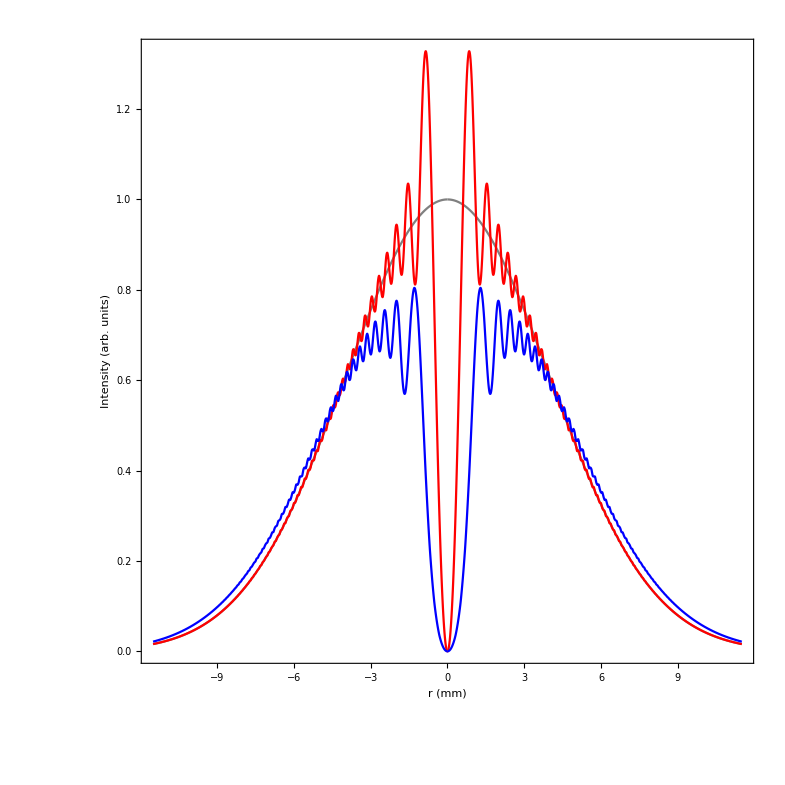

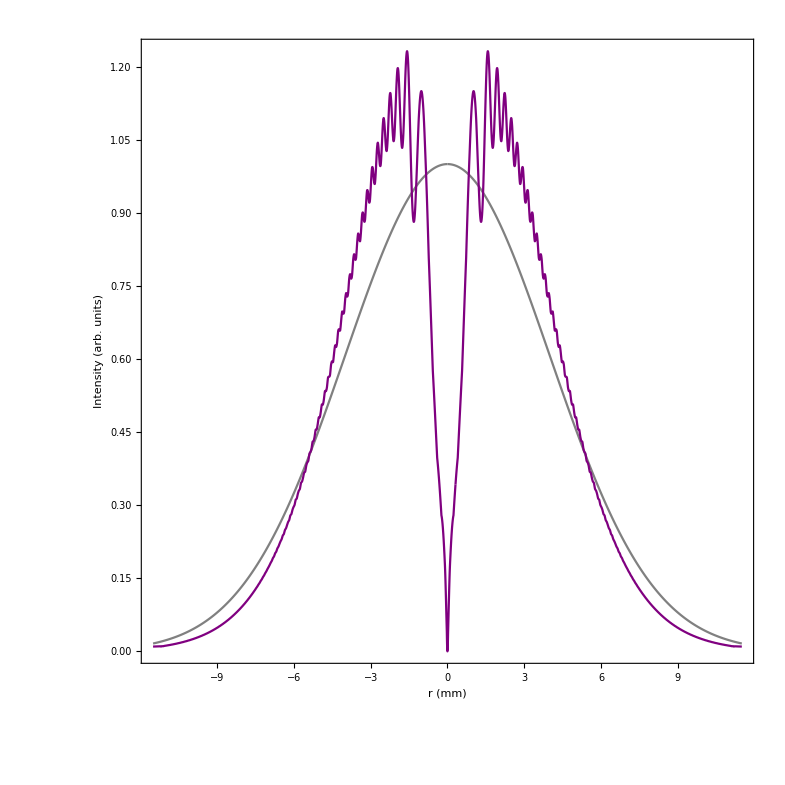

```mathematica
f2b=AmplitudeGeometricOperator[intersection0,intersectionA,"uniformGrid"-> True][f2];
Plot[{Abs[f1[x mm,0]]^2,Abs[f2[x mm,0]]^2,Abs[f2b[x mm,0]]^2},{x,-11.5,11.5},PlotPoints-> 1500,PlotStyle-> {Gray,Red,Blue},FrameLabel->{"r (mm)","Intensity (arb. units)"},PlotRangePadding->{0,Scaled[.05]}]
Plot[{Abs[f1[x mm,0]]^2,Abs[f3[x mm,0]]^2},{x,-11.5,11.5},PlotPoints-> 1500,PlotStyle-> {Gray,Purple},FrameLabel->{"r (mm)","Intensity (arb. units)"},PlotRangePadding->{0,Scaled[.05]}]

(*FIG. 5 - Intensity Profile

Input Gaussian Beam(Gray), the Vortex Beam after 1 m propagation(Red), the Vortex Beam after MC(Blue), the Vortex Beam after the lens(Purple). 
*)
```

```mathematica
Total[Table[x*Abs[f1[x mm,0]]^2,{x,0,18,0.01}]](*This part check the energy conservation. *)
Total[Table[x*Abs[f2[x mm,0]]^2,{x,0,18,0.01}]](*Conservation of energy is fulfilled - accurate Geometrical propagation. *)
Total[Table[x*Abs[f2b[x mm,0]]^2,{x,0,18,0.01}]]
Total[Table[x*Abs[f3[x mm,0]]^2,{x,0,18,0.01}]]
```

1599.93

1599.89

1582.51

1595.07

```mathematica
DensityPlot[Abs[f2[x mm,y mm]]^2,{x,-11.5,11.5},{y,-11.5,11.5},PlotPoints->350,MaxRecursion->1,ColorFunction->spectralCF,PlotRange->All,FrameLabel->{"x (mm)","y (mm)"}]
DensityPlot[If[√(x^2+y^2)≥12,0, Abs[f2b[x mm,y mm]]^2],{x,-11.5,11.5},{y,-11.5,11.5},PlotPoints->350,MaxRecursion->1,ColorFunction->spectralCF,PlotRange->All,FrameLabel->{"x (mm)","y (mm)"}]
DensityPlot[If[√(x^2+y^2)≥12,0, Abs[f3[x mm,y mm]]^2],{x,-11.5,11.5},{y,-11.5,11.5},PlotPoints->350,MaxRecursion->1,ColorFunction->spectralCF,PlotRange->All,FrameLabel->{"x (mm)","y (mm)"}](*FIG. 6 - Density Plot of the Intensity Profile

the Vortex Beam after 1 m propagation(a), the Vortex Beam after MC(b). 
*)
```

```mathematica
(*Checking the expression of Jones Vector for MC given in [11].*)

MatrixForm[MC=({{Cos[θ], -Sin[θ]}, {Sin[θ], Cos[θ]}}).({{1, 0}, {0, ⅈ}}).({{Cos[θ], Sin[θ]}, {-Sin[θ], Cos[θ]}})]//FullSimplify(* x/y polarization states, ideal MC. This is not normalized.*)
MatrixForm[({{1, -ⅈ}, {1, ⅈ}}).MC.({{1, 1}, {ⅈ, -ⅈ}})/(1+ⅈ)]//FullSimplify(* +/- polarization states, ideal MC.  This is not normalized.*)
MatrixForm[MC=({{Cos[θ], -Sin[θ]}, {Sin[θ], Cos[θ]}}).({{Exp[-ⅈ δ], 0}, {0, Exp[ⅈ δ]}}).({{Cos[θ], Sin[θ]}, {-Sin[θ], Cos[θ]}})]//FullSimplify(* x/y polarization states, real MC, δ is characteristic for a ray.*)
MatrixForm[({{1, -ⅈ}, {1, ⅈ}}).MC.({{1, 1}, {ⅈ, -ⅈ}})/2]//FullSimplify(* +/- polarization states, real MC*)
MatrixForm[({{1, -ⅈ}, {1, ⅈ}}).MC.({{1, 1}, {ⅈ, -ⅈ}})/2/.δ-> π/4]//FullSimplify(* δ = convEff/2*)
```

(Cos[θ]^2+ⅈ Sin[θ]^2 | (1-ⅈ) Cos[θ] Sin[θ]
(1-ⅈ) Cos[θ] Sin[θ] | ⅈ Cos[θ]^2+Sin[θ]^2)

(1 | -ⅈ ⅇ^(-2 ⅈ θ)
-ⅈ ⅇ^(2 ⅈ θ) | 1)

(Cos[δ]-ⅈ Cos[2 θ] Sin[δ] | -ⅈ Sin[δ] Sin[2 θ]
-ⅈ Sin[δ] Sin[2 θ] | Cos[δ]+ⅈ Cos[2 θ] Sin[δ])

(Cos[δ] | -ⅈ ⅇ^(-2 ⅈ θ) Sin[δ]
-ⅈ ⅇ^(2 ⅈ θ) Sin[δ] | Cos[δ])

(1/(√2) | -(ⅈ ⅇ^(-2 ⅈ θ))/(√2)
-(ⅈ ⅇ^(2 ⅈ θ))/(√2) | 1/(√2))

```mathematica
(*-Graphics-*)
MatrixForm[MAT=Chop[1/(√2)({{Cos[2 γ], Sin[2γ]}, {Sin[2 γ], -Cos[2 γ]}}).({{Cos[φ]^2+ⅈ Sin[φ]^2, (1-ⅈ) Sin[φ] Cos[φ]}, {(1-ⅈ) Sin[φ] Cos[φ], Sin[φ]^2+ⅈ Cos[φ]^2}}).({{1}, {1}})/.{φ-> 45/180. Pi,γ->  0/180. Pi}//FullSimplify]](*Jonex matrix x/y polarization states, φ gives the orientation of QWP, γ gives the orientation of HWP.*)
MatrixForm[MATxy=Chop[1/(√2)({{1, -ⅈ}, {1, ⅈ}}).MAT]]//FullSimplify(*Jonex matrix +/- polarization states.*)
```

(0.707107
-0.707107)

(0.5+0.5 ⅈ
0.5-0.5 ⅈ)

```mathematica
Rationalize[Chop[(MC/2/.δ-> π/4).MAT//MatrixForm//FullSimplify]]
```

```mathematica
({{1/(√2), +1/(√2)}, {-1/(√2), 1/(√2)}}).({{1/4-1/4 ⅈ Cos[2 θ]+1/2 ⅈ Cos[θ] Sin[θ]}, {-1/4-1/4 ⅈ Cos[2 θ]-1/2 ⅈ Cos[θ] Sin[θ]}})//MatrixForm//FullSimplify(*The x/y Jones vector of the beam after the Polarization Rotator considering with φ-> 45/180. Pi,γ->  0/180. Pi. *)
```

(-(ⅈ Cos[2 θ])/(2 √2)
(-1-2 ⅈ Cos[θ] Sin[θ])/(2 √2))

```mathematica
NIntegrate[Abs[-(ⅈ Cos[2 θ])/(2 √2)]^2,{θ,0, 2 π}](*25% of energy - x Polarization.*)
NIntegrate[Abs[(1+2 ⅈ Cos[θ] Sin[θ])/(2 √2)]^2,{θ,0, 2 π}](*75% of energy - y Polarization.*)
(*We will also check what happens in the Focal Plane if use a polarizer (that elliminate the x polarization) placed before and after the Polarization Rotator for this particular (φ-> 45/180. Pi,γ->  0/180. Pi) configuration of QWP, HWP. *)
```

0.392699

1.1781

```mathematica
(*Evaluate this cell once you have elaluated all other cells. Just change the φ-> 90/180. Pi,γ->  0/180. Pi and you will find a different profile in the Focal Plane. *)
MatrixForm[MAT=Chop[1/(√2)({{Cos[2 γ], Sin[2γ]}, {Sin[2 γ], -Cos[2 γ]}}).({{Cos[φ]^2+ⅈ Sin[φ]^2, (1-ⅈ) Sin[φ] Cos[φ]}, {(1-ⅈ) Sin[φ] Cos[φ], Sin[φ]^2+ⅈ Cos[φ]^2}}).({{1}, {1}})/.{φ-> 90/180. Pi,γ->  0/180. Pi}//FullSimplify]](*Jonex matrix x/y polarization states, φ gives the orientation of QWP, γ gives the orientation of HWP.*)
MatrixForm[MATpm=Chop[1/(√2)({{1, -ⅈ}, {1, ⅈ}}).MAT]]//FullSimplify(*Jonex matrix +/- polarization states.*)
fA[x_,y_]=If[x^2+y^2==0,0,(-MAT[[1,1]] y/(√(x^2+y^2))+MAT[[2,1]] x/(√(x^2+y^2)))*f3[x,y]];(*The Azimuthal mode - go to the end of the program to see why. *)
fR[x_,y_]=If[x^2+y^2==0,0,(MAT[[1,1]] x/(√(x^2+y^2))+MAT[[2,1]] y/(√(x^2+y^2)))*f3E[x,y]];(*The Radial mode. *)

(* HERE is the part that computes the Debye-Wolf integral. The expression is slightly changed to take into consideration that the E. Field is evaluated on a plane. *)
(*-Graphics-*)
eikonal[sx_,sy_]=k0*Interpolation[Transpose[{rayTiltFocus,opticalLengthO-MapThread[#1[[1]]*#2[[1]]+#1[[2]]*#2[[2]]&,{rayCoordinateFocus,rayTiltFocus}]}],InterpolationOrder->1][sx,sy];
(* This is to take into consideration the wave-front aberation. *)

(*1A*)(*H[sx_,sy_]:=(({{-Sin[φ]}, {Cos[φ]}, {0}})*fA[-sx focalDistance/√(1-sx^2-sy^2),-sy focalDistance/√(1-sx^2-sy^2)])/.{s-> √(sx^2+sy^2),φ-> ArcTan[sx,sy+0.0000001]}*)
(*These expresions are demonstrated at the end of the program. *)
(*2A*)H[sx_,sy_]:=(({{√2 (√(1-s^2) Cos[φ]-Sin[φ])}, {√2 (Cos[φ]+√(1-s^2) Sin[φ])}, {-√2 s}})*fA[-sx focalDistance/√(1-sx^2-sy^2),-sy focalDistance/√(1-sx^2-sy^2)])/.{s-> √(sx^2+sy^2),φ-> ArcTan[sx,sy+0.0000001]}
(*3A*)(*H[sx_,sy_]:=(({{√2 (-1+√(1-s^2)) Cos[φ] Sin[φ] (Cos[φ]+Sin[φ])}, {-((-1-√(1-s^2)+(-1+√(1-s^2)) Cos[2 φ]) (Cos[φ]+Sin[φ]))/(√2)}, {-√2 s Sin[φ] (Cos[φ]+Sin[φ])}})*fA[-sx focalDistance/√(1-sx^2-sy^2),-sy focalDistance/√(1-sx^2-sy^2)])/.{s-> √(sx^2+sy^2),φ-> ArcTan[sx,sy+0.0000001]}*)
(*4A*)(*H[sx_,sy_]:=(({{(Cos[φ] (1+√(1-s^2)+(-1+√(1-s^2)) Cos[2 φ]+(-1+√(1-s^2)) Sin[2 φ]))/(√2)}, {(Cos[φ] (1+√(1-s^2)-(-1+√(1-s^2)) Cos[2 φ]+(-1+√(1-s^2)) Sin[2 φ]))/(√2)}, {-√2 s Cos[φ] (Cos[φ]+Sin[φ])}})*fA[-sx focalDistance/√(1-sx^2-sy^2),-sy focalDistance/√(1-sx^2-sy^2)])/.{s-> √(sx^2+sy^2),φ-> ArcTan[sx,sy+0.0000001]}*)

Clear[eX,eY,eZ]
eX[sx_,sy_]=H[sx,sy][[1,1]];
eY[sx_,sy_]=H[sx,sy][[2,1]];
eZ[sx_,sy_]=H[sx,sy][[3,1]];

clearApRad=11.5 mm;(*Clear aperture radius.*)
sMax=clearApRad/(√(clearApRad^2+focalDistance^2));
Ex[sT_]:=0;
Ey[sT_]:=0;
Ez[sT_]:=0;
Ex[sT_?(√(#[[1]]^2+#[[2]]^2)≤ sMax&)]:=Exp[ⅈ eikonal[sT[[1]],sT[[2]]]]eX[sT[[1]],sT[[2]]]/(√(1-sT[[1]]^2-sT[[2]]^2))^2;
Ey[sT_?(√(#[[1]]^2+#[[2]]^2)≤ sMax&)]:=Exp[ⅈ eikonal[sT[[1]],sT[[2]]]]eY[sT[[1]],sT[[2]]]/(√(1-sT[[1]]^2-sT[[2]]^2))^2;
Ez[sT_?(√(#[[1]]^2+#[[2]]^2)≤ sMax&)]:=Exp[ⅈ eikonal[sT[[1]],sT[[2]]]]eZ[sT[[1]],sT[[2]]]/(√(1-sT[[1]]^2-sT[[2]]^2))^2;


wWDP=(2*clearApRad)/(√(4*clearApRad^2+focalDistance^2));

nWDP=256;
Clear[FTf1,FTf2,FTf3]
dkx=2π/(2.wWDP*k0);
FTf1:=Transpose[RotateRight[Transpose[RotateRight[Fourier[Transpose[RotateLeft[Transpose[RotateLeft[Table[N@Ex[{sx,sy}],{sx,-wWDP+2wWDP/nWDP,wWDP,2wWDP/nWDP},{sy,-wWDP+2wWDP/nWDP,wWDP,2wWDP/nWDP}],nWDP/2-1]],nWDP/2-1]]],nWDP/2-1]],nWDP/2-1]];
FTf2:=Transpose[RotateRight[Transpose[RotateRight[Fourier[Transpose[RotateLeft[Transpose[RotateLeft[Table[N@Ey[{sx,sy}],{sx,-wWDP+2wWDP/nWDP,wWDP,2wWDP/nWDP},{sy,-wWDP+2wWDP/nWDP,wWDP,2wWDP/nWDP}],nWDP/2-1]],nWDP/2-1]]],nWDP/2-1]],nWDP/2-1]];
FTf3:=Transpose[RotateRight[Transpose[RotateRight[Fourier[Transpose[RotateLeft[Transpose[RotateLeft[Table[N@Ez[{sx,sy}],{sx,-wWDP+2wWDP/nWDP,wWDP,2wWDP/nWDP},{sy,-wWDP+2wWDP/nWDP,wWDP,2wWDP/nWDP}],nWDP/2-1]],nWDP/2-1]]],nWDP/2-1]],nWDP/2-1]];

Clear[aa1,aa2,aa3]
Timing[aa1=FTf1][[1]]
Timing[aa2=FTf2][[1]]
Timing[aa3=FTf3][[1]]
EXA=ListInterpolation[aa1,{{-dkx*(nWDP/2-1),dkx*nWDP/2},{-dkx*(nWDP/2-1),dkx*nWDP/2}},InterpolationOrder->10]
EYA=ListInterpolation[aa2,{{-dkx*(nWDP/2-1),dkx*nWDP/2},{-dkx*(nWDP/2-1),dkx*nWDP/2}},InterpolationOrder->10]
EZA=ListInterpolation[aa3,{{-dkx*(nWDP/2-1),dkx*nWDP/2},{-dkx*(nWDP/2-1),dkx*nWDP/2}},InterpolationOrder->10]

eikonal[sx_,sy_]=k0*Interpolation[Transpose[{rayTiltFocus,opticalLengthE-MapThread[#1[[1]]*#2[[1]]+#1[[2]]*#2[[2]]&,{rayCoordinateFocus,rayTiltFocus}]}],InterpolationOrder->1][sx,sy];

(*1R*)(*H[sx_,sy_]:=(({{√(1-s^2) Cos[φ]}, {√(1-s^2) Sin[φ]}, {-s}})*fR[-sx focalDistance/√(1-sx^2-sy^2),-sy focalDistance/√(1-sx^2-sy^2)])/.{s-> √(sx^2+sy^2),φ-> ArcTan[sx,sy+0.0000001]}*)
(*2R*)H[sx_,sy_]:=(({{√2 (√(1-s^2) Cos[φ]+Sin[φ])}, {√2 (-Cos[φ]+√(1-s^2) Sin[φ])}, {-√2 s}})*fR[-sx focalDistance/√(1-sx^2-sy^2),-sy focalDistance/√(1-sx^2-sy^2)])/.{s-> √(sx^2+sy^2),φ-> ArcTan[sx,sy+0.0000001]}
(*3R*)(*H[sx_,sy_]:=(({{-√2 (-1+√(1-s^2)) Cos[φ] (Cos[φ]-Sin[φ]) Sin[φ]}, {((-1-√(1-s^2)+(-1+√(1-s^2)) Cos[2 φ]) (Cos[φ]-Sin[φ]))/(√2)}, {√2 s (Cos[φ]-Sin[φ]) Sin[φ]}})*fR[-sx focalDistance/√(1-sx^2-sy^2),-sy focalDistance/√(1-sx^2-sy^2)])/.{s-> √(sx^2+sy^2),φ-> ArcTan[sx,sy+0.0000001]}*)
(*4R*)(*H[sx_,sy_]:=(({{(Sin[φ] (1+√(1-s^2)+(-1+√(1-s^2)) Cos[2 φ]+(-1+√(1-s^2)) Sin[2 φ]))/(√2)}, {(Sin[φ] (1+√(1-s^2)-(-1+√(1-s^2)) Cos[2 φ]+(-1+√(1-s^2)) Sin[2 φ]))/(√2)}, {-√2 s Sin[φ] (Cos[φ]+Sin[φ])}})*fR[-sx focalDistance/√(1-sx^2-sy^2),-sy focalDistance/√(1-sx^2-sy^2)])/.{s-> √(sx^2+sy^2),φ-> ArcTan[sx,sy+0.0000001]}*)

Clear[eX,eY,eZ]
eX[sx_,sy_]=H[sx,sy][[1,1]];
eY[sx_,sy_]=H[sx,sy][[2,1]];
eZ[sx_,sy_]=H[sx,sy][[3,1]];

clearApRad=11.5 mm;(*Clear aperture radius.*)
sMax=clearApRad/(√(clearApRad^2+focalDistance^2));
Ex[sT_]:=0;
Ey[sT_]:=0;
Ez[sT_]:=0;
Ex[sT_?(√(#[[1]]^2+#[[2]]^2)≤ sMax&)]:=Exp[ⅈ eikonal[sT[[1]],sT[[2]]]]eX[sT[[1]],sT[[2]]]/(√(1-sT[[1]]^2-sT[[2]]^2))^2;
Ey[sT_?(√(#[[1]]^2+#[[2]]^2)≤ sMax&)]:=Exp[ⅈ eikonal[sT[[1]],sT[[2]]]]eY[sT[[1]],sT[[2]]]/(√(1-sT[[1]]^2-sT[[2]]^2))^2;
Ez[sT_?(√(#[[1]]^2+#[[2]]^2)≤ sMax&)]:=Exp[ⅈ eikonal[sT[[1]],sT[[2]]]]eZ[sT[[1]],sT[[2]]]/(√(1-sT[[1]]^2-sT[[2]]^2))^2;


wWDP=(2*clearApRad)/(√(4*clearApRad^2+focalDistance^2));

nWDP=256;
Clear[FTf1,FTf2,FTf3]
dkx=2π/(2.wWDP*k0);
FTf1:=Transpose[RotateRight[Transpose[RotateRight[Fourier[Transpose[RotateLeft[Transpose[RotateLeft[Table[N@Ex[{sx,sy}],{sx,-wWDP+2wWDP/nWDP,wWDP,2wWDP/nWDP},{sy,-wWDP+2wWDP/nWDP,wWDP,2wWDP/nWDP}],nWDP/2-1]],nWDP/2-1]]],nWDP/2-1]],nWDP/2-1]];
FTf2:=Transpose[RotateRight[Transpose[RotateRight[Fourier[Transpose[RotateLeft[Transpose[RotateLeft[Table[N@Ey[{sx,sy}],{sx,-wWDP+2wWDP/nWDP,wWDP,2wWDP/nWDP},{sy,-wWDP+2wWDP/nWDP,wWDP,2wWDP/nWDP}],nWDP/2-1]],nWDP/2-1]]],nWDP/2-1]],nWDP/2-1]];
FTf3:=Transpose[RotateRight[Transpose[RotateRight[Fourier[Transpose[RotateLeft[Transpose[RotateLeft[Table[N@Ez[{sx,sy}],{sx,-wWDP+2wWDP/nWDP,wWDP,2wWDP/nWDP},{sy,-wWDP+2wWDP/nWDP,wWDP,2wWDP/nWDP}],nWDP/2-1]],nWDP/2-1]]],nWDP/2-1]],nWDP/2-1]];

Clear[aa1,aa2,aa3]
Timing[aa1=FTf1][[1]]
Timing[aa2=FTf2][[1]]
Timing[aa3=FTf3][[1]]
EXR=ListInterpolation[aa1,{{-dkx*(nWDP/2-1),dkx*nWDP/2},{-dkx*(nWDP/2-1),dkx*nWDP/2}},InterpolationOrder->10]
EYR=ListInterpolation[aa2,{{-dkx*(nWDP/2-1),dkx*nWDP/2},{-dkx*(nWDP/2-1),dkx*nWDP/2}},InterpolationOrder->10]
EZR=ListInterpolation[aa3,{{-dkx*(nWDP/2-1),dkx*nWDP/2},{-dkx*(nWDP/2-1),dkx*nWDP/2}},InterpolationOrder->10]
```

(0.+0.707107 ⅈ
-0.707107)

(0.+1. ⅈ
0)

6.0625

6.29688

5.85938

InterpolatingFunction[{{-0.000065862, 0.0000663806}, {-0.000065862, 0.0000663806}}, <>]

InterpolatingFunction[{{-0.000065862, 0.0000663806}, {-0.000065862, 0.0000663806}}, <>]

InterpolatingFunction[{{-0.000065862, 0.0000663806}, {-0.000065862, 0.0000663806}}, <>]

5.96875

6.09375

5.79688

InterpolatingFunction[{{-0.000065862, 0.0000663806}, {-0.000065862, 0.0000663806}}, <>]

InterpolatingFunction[{{-0.000065862, 0.0000663806}, {-0.000065862, 0.0000663806}}, <>]

InterpolatingFunction[{{-0.000065862, 0.0000663806}, {-0.000065862, 0.0000663806}}, <>]

```mathematica
focalSpotY=DensityPlot[Abs[EYR[x um,y um]+EYA[x um,y um]],{x,-3.5,3.5},{y,-3.5,3.5},ColorFunction->spectralCF,PlotRange-> All,PlotPoints-> 150,MaxRecursion-> 1](*Independent components of the E. Fild. *)
```

```mathematica
focalSpotT=DensityPlot[(Abs[EXR[x um,y um]+EXA[x um,y um]]^2+Abs[EYR[x um,y um]+EYA[x um,y um]]^2+Abs[EZR[x um,y um]+EZA[x um,y um]]^2),{x,-3.5,3.5},{y,-3.5,3.5},ColorFunction->spectralCF,PlotRange-> All,PlotPoints-> 250,MaxRecursion-> 1]
(*Focal Spot Profile. *)
```

```mathematica
coord=Table[{y um,-x um},{x,-3.5,3.5,2 3.5/584},{y,-3.5,3.5,2 3.5/584}];
STED=Map[(Abs[EXR[#[[1]],#[[2]]]+EXA[#[[1]],#[[2]]]]^2+Abs[EYR[#[[1]],#[[2]]]+EYA[#[[1]],#[[2]]]]^2+Abs[EZR[#[[1]],#[[2]]]+EZA[#[[1]],#[[2]]]]^2)&,coord,{2}];
PUMP=Map[Exp[-2(#[[1]]^2+#[[2]]^2)/(0.9 um)^2]&,coord,{2}];
ISATR=12;(*Ratio between the maxIntensity of the Focal Spot and Saturation Intensity of the probe. *)
PIF=Colorize[ImageAdjust@Image[PUMP Exp[-ISATR STED/Max[STED]]],ColorFunction->hotCF]
(*Point Image Function of a STED Microscope assuming a 1.8 μm diameter Gaussian Pump Beam. *)
```

```mathematica
(*FIG. 7 - Density Plot of the Intensity Profile

in the Focal Plane for various configurations and the Point Image Function for some of them . 
*)
```

```mathematica
{φ-> 10/180. Pi,γ->  5/180. Pi}(*The first matrix is the Jones Vector in the x/y basis and the second is the Jones Vector in the +/- basis for the beam before MC. *)
({{0.81915}, {-0.57357 ⅈ}})
({{0.17365}, {0.98481}})
```

```mathematica
{φ-> 0/180. Pi,γ->  0/180. Pi}(**)
({{√2}, {-√2 ⅈ}})
({{0}, {1}})
```

```mathematica
{φ-> 45/180. Pi,γ->  22.5/180. Pi}
({{1}, {0}})
({{√2}, {√2}})
```

```mathematica
{φ-> 45/180. Pi,γ->  0/180. Pi}
({{√2}, {-√2}})
({{1/2+ⅈ/2}, {1/2-ⅈ/2}})
```

```mathematica
(*This is the Point Image Function for the above STED Focal Spot, IRSAT=12.*)
```

```mathematica
(*This is the Focal Spot for {φ-> 45/180. Pi,γ->  0/180. Pi} considering a linear polarizer placed after the Polarization Rotator. *)
(*For this configuration comment the lines 2A and 2R and de-comment the lines 3A and 3R. *)
```

```mathematica
(*This is the Focal Spot for {φ-> 45/180. Pi,γ->  0/180. Pi} considering a linear polarizer placed before the Polarization Rotator, after MC. *)
(*For this configuration comment the lines 2A and 2R and de-comment the lines 4A and 4R. *)
```

```mathematica
(*This is the Point Image Function for the above STED Focal Spot, IRSAT=12.*)
```

```mathematica
{φ-> 90/180. Pi,γ->  0/180. Pi}
({{√2 ⅈ}, {-√2}})
({{ⅈ}, {0}})
```

```mathematica
(*This is the Point Image Function for the above STED Focal Spot, IRSAT=12.*)
```

```mathematica
xA=(({{-Sin[θ], Cos[θ]}}).({{1}, {0}}))[[1,1]]//FullSimplify(*These are the projections of Azimuthal/Radial vectors on x/y*)
xR=(({{Cos[θ], Sin[θ]}}).({{1}, {0}}))[[1,1]]//FullSimplify
yA=(({{-Sin[θ], Cos[θ]}}).({{0}, {1}}))[[1,1]]//FullSimplify
yR=(({{Cos[θ], Sin[θ]}}).({{0}, {1}}))[[1,1]]//FullSimplify
```

-Sin[θ]

Cos[θ]

Cos[θ]

Sin[θ]

```mathematica
(*Please note the folowing identities: *)
(*Sin[θ] = Sin[ArcTan[x,y]] = y/(√(x^2+y^2))*)
Sin[ArcTan[x,y]] - y/(√(x^2+y^2))
(*Cos[θ] = Cos[ArcTan[x,y]] = x/(√(x^2+y^2))*)
Cos[ArcTan[x,y]] - x/(√(x^2+y^2))
```

0

0

```mathematica
(*This was used to define the modes fA and fR depending on the Jones vector of the beam incoming on the MC. *)
```

```mathematica
(*The Matrix ℒ.({{Jx}, {Jy}}) give the components of ({{Ex}, {Ey}, {Ez}}) of the E. Field in the Plane of the Lens according to the Debye-Wolf Diffraction formula: *)
(* E. Wolf, and D. Gabor, "Electromagnetic di.0braction in optical systems — I. An integral representation of the image field," Proc.R.Soc.Lond. 253, 349–357 (1997). *)

ℒ=({{1+√(1-s^2)-Cos[2 φ](1-√(1-s^2)), -Sin[2 φ](1-√(1-s^2))}, {-Sin[2 φ](1-√(1-s^2)), 1+√(1-s^2)+Cos[2 φ](1-√(1-s^2))}, {-2 Cos[φ]s, -2 Sin[φ] s}});
PR=({{1/(√2), 1/(√2)}, {-1/(√2), 1/(√2)}});(*Jones matrix of the Polarizarion Rotator. *)
```

```mathematica
ℒ.({{-Sin[φ]}, {Cos[φ]}})//FullSimplify//MatrixForm(*This gives the contribution of the Azimuthal mode to the components ({{Ex}, {Ey}, {Ez}}) of the E. Field/ 1A*)
ℒ.({{Cos[φ]}, {Sin[φ]}})//FullSimplify//MatrixForm(*Radial/ 1R*)
ℒ.({{1/(√2), 1/(√2)}, {-1/(√2), 1/(√2)}}).({{-Sin[φ]}, {Cos[φ]}})//FullSimplify//MatrixForm(*This gives the contribution of the Azimuthal mode, before the Polarization Rotator, to the components ({{Ex}, {Ey}, {Ez}}) of the E. Field/ 2A*)
ℒ.({{1/(√2), 1/(√2)}, {-1/(√2), 1/(√2)}}).({{Cos[φ]}, {Sin[φ]}})//FullSimplify//MatrixForm(*Radial/ 2R*)
```

(-2 Sin[φ]
2 Cos[φ]
0)

(2 √(1-s^2) Cos[φ]
2 √(1-s^2) Sin[φ]
-2 s)

(√2 (√(1-s^2) Cos[φ]-Sin[φ])
√2 (Cos[φ]+√(1-s^2) Sin[φ])
-√2 s)

(√2 (√(1-s^2) Cos[φ]+Sin[φ])
√2 (-Cos[φ]+√(1-s^2) Sin[φ])
-√2 s)

```mathematica
ℒ.({{1/(√2), 1/(√2)}, {-1/(√2), 1/(√2)}}).({{0, 0}, {0, 1}}).({{-Sin[φ]}, {Cos[φ]}})//FullSimplify//MatrixForm(*Azimuthal/ 3A. With a Linear Polarizer placed before the Polarization Rotator. *)
ℒ.({{1/(√2), 1/(√2)}, {-1/(√2), 1/(√2)}}).({{0, 0}, {0, 1}}).({{Cos[φ]}, {Sin[φ]}})//FullSimplify//MatrixForm(*Radial/ 3R. With a Linear Polarizer placed before the Polarization Rotator. *)
```

((Cos[φ] (1+√(1-s^2)+(-1+√(1-s^2)) Cos[2 φ]+(-1+√(1-s^2)) Sin[2 φ]))/(√2)
(Cos[φ] (1+√(1-s^2)-(-1+√(1-s^2)) Cos[2 φ]+(-1+√(1-s^2)) Sin[2 φ]))/(√2)
-√2 s Cos[φ] (Cos[φ]+Sin[φ]))

((Sin[φ] (1+√(1-s^2)+(-1+√(1-s^2)) Cos[2 φ]+(-1+√(1-s^2)) Sin[2 φ]))/(√2)
(Sin[φ] (1+√(1-s^2)-(-1+√(1-s^2)) Cos[2 φ]+(-1+√(1-s^2)) Sin[2 φ]))/(√2)
-√2 s Sin[φ] (Cos[φ]+Sin[φ]))

```mathematica
ℒ.({{0, 0}, {0, 1}}).({{1/(√2), 1/(√2)}, {-1/(√2), 1/(√2)}}).({{-Sin[φ]}, {Cos[φ]}})//FullSimplify//MatrixForm(*Azimuthal/ 4A. With a Linear Polarizer placed after the Polarization Rotator (before the Lens). *)
ℒ.({{0, 0}, {0, 1}}).({{1/(√2), 1/(√2)}, {-1/(√2), 1/(√2)}}).({{Cos[φ]}, {Sin[φ]}})//FullSimplify//MatrixForm(*Radial/ 4R. With a Linear Polarizer placed after the Polarization Rotator (before the Lens). *)
```

(√2 (-1+√(1-s^2)) Cos[φ] Sin[φ] (Cos[φ]+Sin[φ])
-((-1-√(1-s^2)+(-1+√(1-s^2)) Cos[2 φ]) (Cos[φ]+Sin[φ]))/(√2)
-√2 s Sin[φ] (Cos[φ]+Sin[φ]))

(-√2 (-1+√(1-s^2)) Cos[φ] (Cos[φ]-Sin[φ]) Sin[φ]
((-1-√(1-s^2)+(-1+√(1-s^2)) Cos[2 φ]) (Cos[φ]-Sin[φ]))/(√2)
√2 s (Cos[φ]-Sin[φ]) Sin[φ])